# Подстановки

x=1 (⇔Set[x,1]    — задание глобального правила)
x→1 (⇔Rule[x,1] — задание локального правила)
x^2/.x→1 (⇔ ReplaceAll[x^2,x→1] — применение локального правила)
x^2+y/.{x→y,y→4}    (однократное применение списка правил)

x^2+y//.{x→y,y→4} (⇔ ReplaceRepeated[…] — полное применение списка правил)
x:>1 (⇔RuleDelayed[x,1] — задание локального правила без вычисления правой части)

```mathematica
x->3
```

x→3

```mathematica
r=x->2
```

x→2

```mathematica
r
```

x→2

```mathematica
x
```

x

```mathematica
?x
```

Global`x

```mathematica
x/.r
```

2

```mathematica
x^2+x-3/.r
```

3

```mathematica
x^2+Sin[x]/.x->√y
```

y+Sin[√y]

```mathematica
a+b/.Plus->Times
```

a b

```mathematica
Times@@(a+b)
```

a b

```mathematica
(a+b)^2/.Plus->Times
```

a^2 b^2

```mathematica
Times@@((a+b)^2)
```

2 (a+b)

?x — список всех правил, асоциированных с x
Clear[x] — очистка правил, ассоциированных с символом

```mathematica
x=1
```

1

```mathematica
?x
```

Global`x

x=1

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
?x
```

Global`x

# Решение Уравнений

a==b (⇔Equal[a,b] — оператор сравнения)

```mathematica
Solve[x^2+x==1,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
Solve[{x^2+y==4,y^2==1},{x,y}]
```

{{x→-√3,y→1},{x→√3,y→1},{x→-√5,y→-1},{x→√5,y→-1}}

```mathematica
sol=Solve[{x^2+y==4,y^2==1},{x,y}];
```

```mathematica
x/.sol
```

{-√3,√3,-√5,√5}

```mathematica
x/.sol⟦3⟧
```

-√5

```mathematica
y/.sol
```

{1,1,-1,-1}

```mathematica
x+2y/.sol
```

{2-√3,2+√3,-2-√5,-2+√5}

Solve[] — решение алгебраического уравнения/системы уравнений аналитичесчими методами
NSolve[] — решение численными методами
FindRoot[] — поиск отдельного корня по начальной точке

```mathematica
Solve[Sin[x]==x/5,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==x/5,x]

```mathematica
NSolve[Sin[x]==x/5,x,Reals]
```

{{x→-2.59574},{x→0.},{x→2.59574}}

```mathematica
FindRoot[{x==Tan[x]-.5},{x,1}]
```

{x→0.975017}

```mathematica
FindRoot[{x==Tan[x]-.5},{x,4.5}]
```

{x→4.51559}

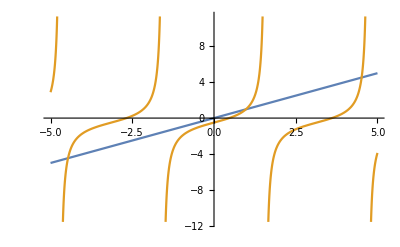

```mathematica
Plot[{x,Tan[x]-1/2},{x,-5,5}]
```

# Параметры графиков

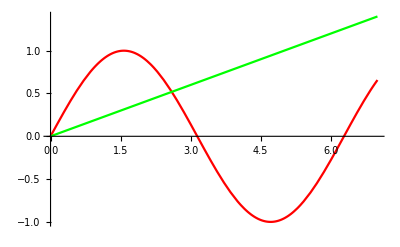

```mathematica
Plot[{Sin[x],x/5},{x,0,7},PlotStyle->{Red,Green}]
```

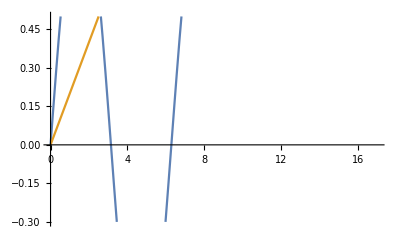

```mathematica
Plot[{Sin[x],x/5},{x,0,7},PlotRange->{{0,17},{-.3,.5}}]
```

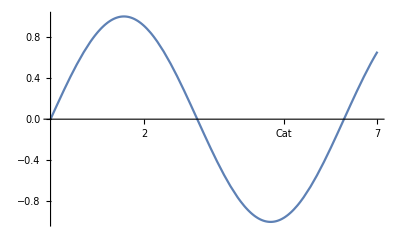

```mathematica
Plot[Sin[x],{x,0,7},Ticks->{{2,{5,"Cat"},7},Automatic}]
```

Полный список настроек в справке функции :

# Задача

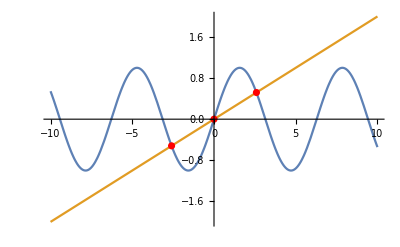

```mathematica
f1[x_]:=Sin[x];f2[x_]:=x/5;

sol=NSolve[f1[x]==f2[x],x,Reals];
list={x,f1[x]}/.sol;
Show[{
Plot[{f1[x],f2[x]},{x,-10,10}],
ListPlot[list,PlotStyle->Red]
},
PlotRange->{{-10,10},{-2,2}}
]
```

```mathematica
ResultPlot[k_]:=Module[{f1,f2,sol,list},

f1[x_]:=Sin[x];f2[x_]:=x/k;
sol=NSolve[{f1[x]==f2[x]},x,Reals];
list={x,f1[x]}/.sol;

Show[{
Plot[{f1[x],f2[x]},{x,-10,10},PlotStyle->{Directive[Thickness[.01],RGBColor[0.15, 0.38, 0.77]],Directive[Thickness[.01],RGBColor[0.9, 0.42, 0.81]]}],
ListPlot[list,PlotStyle->RGBColor[0.32, 1, 0.63],PlotMarkers->{Automatic,14}]
},
PlotRange->{{-10,10},{-2,2}},Method->{"AxesInFront"->False}]
];

Manipulate[ResultPlot[k],{{k,7},1,15}]
```